```mathematica
s={b,c}
norm[x_]:=x.x
x[u_]:=(1+norm[u])/(1-norm[u])
y[u_]:=2 u⟦1⟧/(1-norm[u])
z[u_]:=2 u⟦2⟧/(1-norm[u])
b[u1_,u2_]:=(z[u1] x[u2]-z[u2] x[u1])/(z[u2] y[u1]-z[u1] y[u2])
c[u1_,u2_]:=(y[u2] x[u1]-y[u1] x[u2])/(z[u2] y[u1]-z[u1] y[u2])
center[u1_,u2_]:={-b[u1,u2],-c[u1,u2]}
r[u1_,u2_]:=center[u1,u2].center[u1,u2]-1
Manipulate[Graphics[{{Circle[],Thick,Green,Circle[center[p⟦1⟧,p⟦2⟧],r[p⟦1⟧,p⟦2⟧]]}}],{{p,{{-1/2,-1/2},{1/3,-1/3}}},Locator}]
```

{b,c}

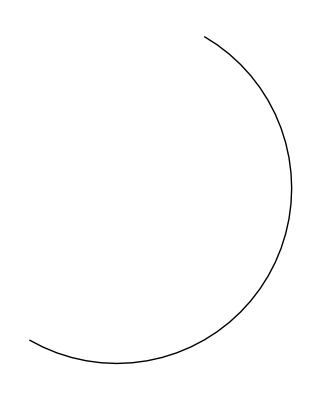

```mathematica
{Graphics[Circle[{0,0},1,{-(20π)/3,-(17π)/3}]]}
```

```mathematica
sol[u1_,u2_]:=s/.Solve[{x[u1]+b*y[u1]+c*z[u1]==0,x[u2]+b*y[u2]+c*z[u2]==0},{b,c}]
```



```mathematica
Graphics[Circle[]]
```

```mathematica
Arccos
```